## Input

This differential equation used here to illustrate this method is of the form 
The user may specify values for A1, A2, A3, which may be functions of x and y, and A4 which may only be a function of x.

```mathematica
mh:=√2;
dmh:=0.01;
mw:=1/(√2);
```

The boundary condition must be specified.

```mathematica
x0=10.0;
y0=0.01;
z0=0.008;
```

```mathematica
xf=1;
yf=1;
zf=10;
```

An initial value for the derivative dy/dx  is assumed and will be adjusted to satisfy the second boundary condition.

```mathematica
dydx1=-0.01;
```

```mathematica
dzdx1=-0.01;
```

An second value for the derivative dy/dx is assumed here as well to be used in second iteration.

```mathematica
dydx2=-10.0;
```

## Setup

To use Runge-Kutta's 4th order method of solving ODEs, the equations must be of order one. Thus, the derivative dy/dx is set equal to another variable and a system of first order differential equations is made. x is rho.

dF/dx = q: This will be function #1, f1 and used for determining k values for the y approximation.

```mathematica
f1[x_,y_,z_,q_,w_]:=q;
```

```mathematica
f2[x_,y_,z_,q_,w_]:=2*mh*q-(mh*z^2)/(4*x);
```

```mathematica
f3[x_,y_,z_,q_,w_]:=w;
```

```mathematica
f4[x_,y_,z_,q_,w_]:=mh*w+(2*z)/x^2-mh/(4*x)*ⅇ^(-mh*x)*y*x;
```

Includes the fact that we go to the left

```mathematica
h=(xf-x0)/20.0
```

-0.45

## First Iteration

```mathematica
X1[0]=x0
Y1[0]=y0
Z1[0]=z0
Q1[0]=dydx1
W1[0]=dzdx1

For[i=0,i<20,i++,
X1[i+1]=X1[i]+h;

k1y=f1[X1[i],Y1[i],Z1[i],Q1[i],W1[i]];
k1z=f2[X1[i],Y1[i],Z1[i],Q1[i],W1[i]];
k1q=f3[X1[i],Y1[i],Z1[i],Q1[i],W1[i]];
k1w=f4[X1[i],Y1[i],Z1[i],Q1[i],W1[i]];

k2y=f1[X1[i]+0.5*h,Y1[i]+0.5*k1y*h,Z1[i]+0.5*k1z*h,Q1[i]+0.5*k1q*h,W1[i]+0.5*k1w*h];
k2z=f2[X1[i]+0.5*h,Y1[i]+0.5*k1y*h,Z1[i]+0.5*k1z*h,Q1[i]+0.5*k1q*h,W1[i]+0.5*k1w*h];
k2q=f3[X1[i]+0.5*h,Y1[i]+0.5*k1y*h,Z1[i]+0.5*k1z*h,Q1[i]+0.5*k1q*h,W1[i]+0.5*k1w*h];
k2w=f4[X1[i]+0.5*h,Y1[i]+0.5*k1y*h,Z1[i]+0.5*k1z*h,Q1[i]+0.5*k1q*h,W1[i]+0.5*k1w*h];

k3y=f1[X1[i]+0.5*h,Y1[i]+0.5*k2y*h,Z1[i]+0.5*k2z*h,Q1[i]+0.5*k2q*h,W1[i]+0.5*k2w*h];
k3z=f2[X1[i]+0.5*h,Y1[i]+0.5*k2y*h,Z1[i]+0.5*k2z*h,Q1[i]+0.5*k2q*h,W1[i]+0.5*k2w*h];
k3q=f3[X1[i]+0.5*h,Y1[i]+0.5*k2y*h,Z1[i]+0.5*k2z*h,Q1[i]+0.5*k2q*h,W1[i]+0.5*k2w*h];
k3w=f4[X1[i]+0.5*h,Y1[i]+0.5*k2y*h,Z1[i]+0.5*k2z*h,Q1[i]+0.5*k2q*h,W1[i]+0.5*k2w*h];

k4y=f1[X1[i]+h,Y1[i]+k3y*h,Z1[i]+k3z*h,Q1[i]+k3q*h,W1[i]+k3w*h];
k4z=f2[X1[i]+h,Y1[i]+k3y*h,Z1[i]+k3z*h,Q1[i]+k3q*h,W1[i]+k3w*h];
k4q=f3[X1[i]+h,Y1[i]+k3y*h,Z1[i]+k3z*h,Q1[i]+k3q*h,W1[i]+k3w*h];
k4w=f4[X1[i]+h,Y1[i]+k3y*h,Z1[i]+k3z*h,Q1[i]+k3q*h,W1[i]+k3w*h];

Y1[i+1]=Y1[i]+1/6*(k1y+2*k2y+2*k3y+k4y)*h;
Z1[i+1]=Z1[i]+1/6*(k1z+2*k2z+2*k3z+k4z)*h;
Q1[i+1]=Q1[i]+1/6*(k1q+2*k2q+2*k3q+k4q)*h;
W1[i+1]=W1[i]+1/6*(k1w+2*k2w+2*k3w+k4w)*h;
]
```

10.

0.01

0.008

-0.01

-0.01

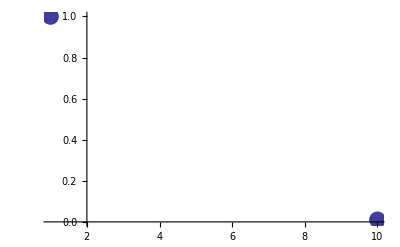

```mathematica
plot1=ListPlot[{{x0,y0},{xf,yf}},PlotStyle->PointSize[0.03]]
```

```mathematica
data1=Table[{X1[i],Y1[i]},{i,0,20}];
data2=Table[{X1[i],Z1[i]},{i,0,20}];
plot2=ListPlot[data1,Joined->True,PlotStyle->{Thickness[0.002],RGBColor[0,1,0]},DisplayFunction->Identity];
plot3=ListPlot[data2,Joined->True,PlotStyle->{Thickness[0.002],RGBColor[1,1,0]},DisplayFunction->Identity];
```

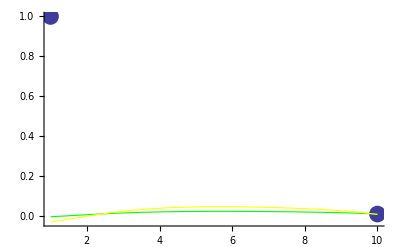

```mathematica
Show[plot1,plot2,plot3,Axes->True,AxesOrigin->{0,0},PlotRange->Automatic]
```

## Section 4: Second Iteration

Now the calculation in the first iteration is repeated but for a different assumed dy/dx at x = x0. This calculation is done the same way as before, but here we have enclosed it in a loop to save space.

```mathematica
X2[0]=x0
Y2[0]=y0
Z2[0]=dydx2
```

0.

2.

-10.

```mathematica
For[i=0,i<5,i++,
X2[i+1]=X2[i]+h;
k1y=f1[X2[i],Y2[i],Z2[i]];
k1z=f2[X2[i],Y2[i],Z2[i]];
k2y=f1[X2[i]+0.5*h,Y2[i]+0.5*k1y*h,Z2[i]+0.5*k1z*h];
k2z=f2[X2[i]+0.5*h,Y2[i]+0.5*k1y*h,Z2[i]+0.5*k1z*h];
k3y=f1[X2[i]+0.5*h,Y2[i]+0.5*k2y*h,Z2[i]+0.5*k2z*h];k3z=f2[X2[i]+0.5*h,Y2[i]+0.5*k2y*h,Z2[i]+0.5*k2z*h];
k4y=f1[X2[i]+h,Y2[i]+k3y*h,Z2[i]+k3z*h];
k4z=f2[X2[i]+h,Y2[i]+k3y*h,Z2[i]+k3z*h];
Y2[i+1]=Y2[i]+1/6*(k1y+2*k2y+2*k3y+k4y)*h;
Z2[i+1]=Z2[i]+1/6*(k1z+2*k2z+2*k3z+k4z)*h
]
```

```mathematica
data=Table[{X2[i],Y2[i]},{i,0,5}];
plot3=ListPlot[data,Joined->True,PlotStyle->{Thickness[0.012],RGBColor[1,1,0]},DisplayFunction->Identity];
```

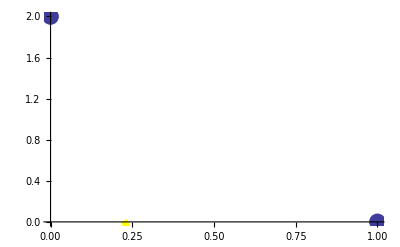

```mathematica
Show[plot1,plot2,plot3]
```

## Section 5: Third Iteration

By examining the figure immediately above, you will note that at x = x0, the solution (for both iterations) is close to the boundary condition. At x = xf  however, it is likely that the solution does not (unless you are a good guesser). We can use the first two iterations to predict what a better value for dy/dx should be. We will assume that the relationship is linear and use interpolation to determine the final estimate for dy/dx. This will yield exact results if the equation is linear while for nonlinear differential equations it will be a reasonable approximation.

The third assumed dy/dx.

```mathematica
dydx3=(dydx1-dydx2)/(Y1[5]-Y2[5])*(yf-Y2[5])+dydx2
```

5.67591

```mathematica
X3[0]=x0
Y3[0]=y0
Z3[0]=dydx3
```

0.

2.

5.67591

As in the second iteration we are doing this calculation in a loop.

```mathematica
For[i=0,i<5,i++,
X3[i+1]=X3[i]+h;
k1y=f1[X3[i],Y3[i],Z3[i]];
k1z=f2[X3[i],Y3[i],Z3[i]];
k2y=f1[X3[i]+0.5*h,Y3[i]+0.5*k1y*h,Z3[i]+0.5*k1z*h];
k2z=f2[X3[i]+0.5*h,Y3[i]+0.5*k1y*h,Z3[i]+0.5*k1z*h];
k3y=f1[X3[i]+0.5*h,Y3[i]+0.5*k2y*h,Z3[i]+0.5*k2z*h];k3z=f2[X3[i]+0.5*h,Y3[i]+0.5*k2y*h,Z3[i]+0.5*k2z*h];
k4y=f1[X3[i]+h,Y3[i]+k3y*h,Z3[i]+k3z*h];
k4z=f2[X3[i]+h,Y3[i]+k3y*h,Z3[i]+k3z*h];
Y3[i+1]=Y3[i]+1/6*(k1y+2*k2y+2*k3y+k4y)*h;
Z3[i+1]=Z3[i]+1/6*(k1z+2*k2z+2*k3z+k4z)*h
]
```

```mathematica
data=Table[{X3[i],Y3[i]},{i,0,5}];
plot4=ListPlot[data,Joined->True,PlotStyle->{Thickness[0.012],RGBColor[1,0,0]},DisplayFunction->Identity];
```

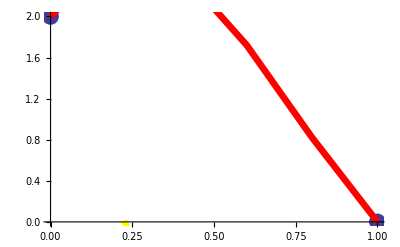

```mathematica
Show[plot1,plot2,plot3,plot4]
```